```mathematica
Quit[];
```

# FeynArts & FeynCalc Amplitude Calculations

## Loading Packages

```mathematica
$LoadAddOns={"FeynArtsLoader"};
```

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True];
```

Patched 2 FeynArts models.

## Basics

#### Topologies

```mathematica
t12=CreateTopologies[0,1->2];
t22=CreateTopologies[0,2->2];
```

## e^+ e^--> γ γ

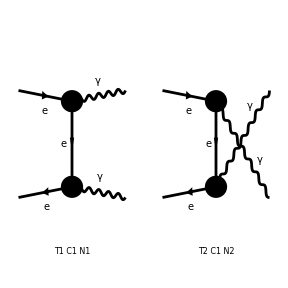

```mathematica
feeγγ=InsertFields[t22,{F[2,{1}],-F[2,{1}]}->{V[1],V[1]},ExcludeParticles->F[_,{2|3}],InsertionLevel->{Classes}];
Paint[%];
```

```mathematica
Aeeγγ=CreateFeynAmp[feeγγ]/.FAPropagatorDenominator[FourMomentum[Incoming,2]-FourMomentum[Outgoing,2],FCGV["ME"]]->1/t/.FAPropagatorDenominator[FourMomentum[Incoming,2]-FourMomentum[Outgoing,1],FCGV["ME"]]->1/u;
```

```mathematica
FCFAConvert[Aeeγγ,IncomingMomenta->{p1,p2},OutgoingMomenta->{q1,q2},DropSumOver->True,LorentzIndexNames->{μ,ν}]
DiracSimplify[%,DiracSubstitute67->True]//Simplify
```

{(((ε̄)^*)^μ(q1) ((ε̄)^*)^ν(q2) (φ(-OverBar[p2],FCGV(ME))).(ⅈ FCGV(EL) (γ̄)^ν.(γ̄)^6+ⅈ FCGV(EL) (γ̄)^ν.(γ̄)^7).(γ̄·(OverBar[q2]-OverBar[p2])+FCGV(ME)).(ⅈ FCGV(EL) (γ̄)^μ.(γ̄)^6+ⅈ FCGV(EL) (γ̄)^μ.(γ̄)^7).(φ(OverBar[p1],FCGV(ME))))/t,(((ε̄)^*)^μ(q1) ((ε̄)^*)^ν(q2) (φ(-OverBar[p2],FCGV(ME))).(ⅈ FCGV(EL) (γ̄)^μ.(γ̄)^6+ⅈ FCGV(EL) (γ̄)^μ.(γ̄)^7).(γ̄·(OverBar[q1]-OverBar[p2])+FCGV(ME)).(ⅈ FCGV(EL) (γ̄)^ν.(γ̄)^6+ⅈ FCGV(EL) (γ̄)^ν.(γ̄)^7).(φ(OverBar[p1],FCGV(ME))))/u}

{-((FCGV(EL))^2 ((φ(-OverBar[p2],FCGV(ME))).(γ̄·(ε̄)^*(q2)).(γ̄·OverBar[q2]).(γ̄·(ε̄)^*(q1)).(φ(OverBar[p1],FCGV(ME)))-2 (OverBar[p2]·(ε̄)^*(q2)) (φ(-OverBar[p2],FCGV(ME))).(γ̄·(ε̄)^*(q1)).(φ(OverBar[p1],FCGV(ME)))))/t,-((FCGV(EL))^2 ((φ(-OverBar[p2],FCGV(ME))).(γ̄·(ε̄)^*(q1)).(γ̄·OverBar[q1]).(γ̄·(ε̄)^*(q2)).(φ(OverBar[p1],FCGV(ME)))-2 (OverBar[p2]·(ε̄)^*(q1)) (φ(-OverBar[p2],FCGV(ME))).(γ̄·(ε̄)^*(q2)).(φ(OverBar[p1],FCGV(ME)))))/u}

## e^+ e^--> μ^+ μ^-

loading generic model file /home/serner/.Mathematica/Applications/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/serner/.Mathematica/Applications/FeynCalc/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Classes insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

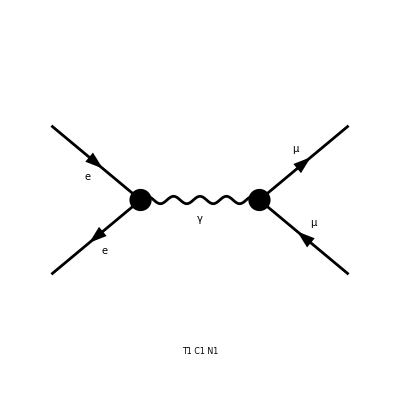

```mathematica
feeμμ=InsertFields[t22,{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]},InsertionLevel->{Classes},
	ExcludeParticles->{V[2],S[1],S[2]}];
Paint[%];
```

```mathematica
Aeeμμ=CreateFeynAmp[DiagramExtract[feeμμ,1]]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

FAFeynAmpList(Process→(F(2,{1}) | p1 | FCGV(ME) | {-Charge,LeptonNumber}
-F(2,{1}) | p2 | FCGV(ME) | {Charge,-LeptonNumber})→(F(2,{2}) | k1 | FCGV(MM) | {-Charge,LeptonNumber}
-F(2,{2}) | k2 | FCGV(MM) | {Charge,-LeptonNumber}),Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Classes},ExcludeParticles→{S(1),S(2),V(2)},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Classes==1,Number==1),Integral[],1/(k1+k2)^2 g(Lor1,Lor2) ū(k1,FCGV(MM)).(ⅈ FCGV(EL) ga(Lor2).om_-+ⅈ FCGV(EL) ga(Lor2).om_+).v(k2,FCGV(MM)) v̄(p2,FCGV(ME)).(ⅈ FCGV(EL) ga(Lor1).om_-+ⅈ FCGV(EL) ga(Lor1).om_+).u(p1,FCGV(ME))))

## No Spin

```mathematica
FCFAConvert[Aeeμμ,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},DropSumOver->True,LorentzIndexNames->{μ,ν}]/.FCGV["ME"]->me/.FCGV["MM"]->mμ/.FCGV["EL"]->e
DiracSimplify[%,DiracSubstitute67->True]//Simplify
Total[%]//Simplify
1/4*FermionSpinSum[Contract[%ComplexConjugate[%]]]//DiracSimplify//Simplify
%/.s->4*Ebeam^2/.t->me^2+mμ^2+2*(Ebeam^2-Ebeam*Sqrt[Ebeam^2-mμ^2]*Cos[θ])/.u->me^2+mμ^2+2*(Ebeam^2+Ebeam*Sqrt[Ebeam^2-mμ^2]*Cos[θ])//Simplify
%/.me->0//Simplify
(%-e^4*((1+mμ^2/Ebeam^2)+(1-mμ^2/Ebeam^2)*Cos[θ]^2))//Simplify
```

{((ḡ)^μν (φ(-OverBar[p2],me)).(ⅈ e (γ̄)^μ.(γ̄)^6+ⅈ e (γ̄)^μ.(γ̄)^7).(φ(OverBar[p1],me)) (φ(OverBar[p3],mμ)).(ⅈ e (γ̄)^ν.(γ̄)^6+ⅈ e (γ̄)^ν.(γ̄)^7).(φ(-OverBar[p4],mμ)))/(OverBar[p3]+OverBar[p4])^2}

{-(e^2 (φ(-OverBar[p2],me)).(γ̄)^μ.(φ(OverBar[p1],me)) (φ(OverBar[p3],mμ)).(γ̄)^μ.(φ(-OverBar[p4],mμ)))/(OverBar[p3]+OverBar[p4])^2}

-(e^2 (φ(-OverBar[p2],me)).(γ̄)^μ.(φ(OverBar[p1],me)) (φ(OverBar[p3],mμ)).(γ̄)^μ.(φ(-OverBar[p4],mμ)))/(OverBar[p3]+OverBar[p4])^2

8 e^4 (1/(OverBar[p3]+OverBar[p4])^2)^2 (me^2 (OverBar[p3]·OverBar[p4])+mμ^2 (OverBar[p1]·OverBar[p2])+(OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3])+(OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p4])+2 me^2 mμ^2)

8 e^4 (1/(OverBar[p3]+OverBar[p4])^2)^2 (me^2 (OverBar[p3]·OverBar[p4])+mμ^2 (OverBar[p1]·OverBar[p2])+(OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3])+(OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p4])+2 me^2 mμ^2)

8 e^4 (1/(OverBar[p3]+OverBar[p4])^2)^2 (mμ^2 (OverBar[p1]·OverBar[p2])+(OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3])+(OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p4]))

e^4 (8 (1/(OverBar[p3]+OverBar[p4])^2)^2 (mμ^2 (OverBar[p1]·OverBar[p2])+(OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3])+(OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p4]))-((Ebeam^2-mμ^2) cos^2(θ)+Ebeam^2+mμ^2)/Ebeam^2)

## With Spin

```mathematica
FCFAConvert[Aeeμμ,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},DropSumOver->True,LorentzIndexNames->{μ,ν}]/.FCGV["ME"]->me/.FCGV["MM"]->mμ/.FCGV["EL"]->e;
DiracSimplify[%,DiracSubstitute67->True]//Simplify
(1/2)^4*%/.Spinor[Momentum[p1],me,1]->(1+s1*DiracGamma[5]).Spinor[Momentum[p1],me,1]/.Spinor[Momentum[p3],mμ,1]->Spinor[Momentum[p3],mμ,1].(1-s3*DiracGamma[5])/.Spinor[-Momentum[p2],me,1]->Spinor[-Momentum[p2],me,1].(1-s2*DiracGamma[5])/.Spinor[-Momentum[p4],mμ,1]->(1+s4*DiracGamma[5]).Spinor[-Momentum[p4],mμ,1]//Simplify;
Total[%]//DiracSimplify//Simplify
Simplify[FermionSpinSum[Contract[%ComplexConjugate[%]]]//DiracSimplify]/.(s1)^2->1/.(s2)^2->1/.(s3)^2->1/.(s4)^2->1//Simplify
test1=%/.s->4*Ebeam^2/.t->me^2+mμ^2+2*(Ebeam^2-Ebeam*Sqrt[Ebeam^2-mμ^2]*Cos[θ])/.u->me^2+mμ^2+2*(Ebeam^2+Ebeam*Sqrt[Ebeam^2-mμ^2]*Cos[θ])//Simplify
```

{-(e^2 (φ(-OverBar[p2],me)).(γ̄)^μ.(φ(OverBar[p1],me)) (φ(OverBar[p3],mμ)).(γ̄)^μ.(φ(-OverBar[p4],mμ)))/s}

-(e^2 ((s1 s2+1) (φ(-OverBar[p2],me)).(γ̄)^μ.(φ(OverBar[p1],me))+(s1+s2) (φ(-OverBar[p2],me)).(γ̄)^μ.(γ̄)^5.(φ(OverBar[p1],me))) ((s3 s4+1) (φ(OverBar[p3],mμ)).(γ̄)^μ.(φ(-OverBar[p4],mμ))+(s3+s4) (φ(OverBar[p3],mμ)).(γ̄)^μ.(γ̄)^5.(φ(-OverBar[p4],mμ))))/(16 s)

1/(2 s^2)e^4 (2 me^4 (s1 s2+1) (s3 s4+1)+2 me^2 (mμ^2 (s1 s2 (s3+s4)^2+2 s3 s4+2)+t (s1 (-s2 (s3 s4+1)+s3+s4)+s2 (s3+s4)-s3 s4-1)-u (s1 (s2 s3 s4+s2+s3+s4)+s2 (s3+s4)+s3 s4+1))+2 mμ^4 (s1 s2+1) (s3 s4+1)-2 mμ^2 (t (s1 (s2 s3 s4+s2-s3-s4)-s2 (s3+s4)+s3 s4+1)+u (s1 (s2 s3 s4+s2+s3+s4)+s2 (s3+s4)+s3 s4+1))+s1 s2 s3 s4 t^2+s1 s2 s3 s4 u^2+s1 s2 t^2+s1 s2 u^2-s1 s3 t^2+s1 s3 u^2-s1 s4 t^2+s1 s4 u^2-s2 s3 t^2+s2 s3 u^2-s2 s4 t^2+s2 s4 u^2+s3 s4 t^2+s3 s4 u^2+t^2+u^2)

(e^4 (4 Ebeam^4 (s1 s2+1) (s3 s4+1)+4 Ebeam^2 (Ebeam^2-mμ^2) cos^2(θ) (s1 s2+1) (s3 s4+1)+8 Ebeam^3 √(Ebeam^2-mμ^2) cos(θ) (s1+s2) (s3+s4)+me^2 mμ^2 s1 s2 (s3^2+s4^2-2)))/(16 Ebeam^4)

```mathematica
test1/.s1->+1/.s2->-1/.s3->+1/.s4->-1//Simplify
```

0

```mathematica
Simplify[test1/.s1->+1/.s2->+1/.s3->+1/.s4->+1,Assumptions->Ebeam>=0]
Simplify[%/.mμ->0,Assumptions->Ebeam>=0];
(%-e^4*(1+Cos[θ])^2)//Simplify
Simplify[test1/.s1->+1/.s2->+1/.s3->-1/.s4->-1,Assumptions->Ebeam>=0]
Simplify[%/.mμ->0,Assumptions->Ebeam>=0];
(%-e^4*(1-Cos[θ])^2)//Simplify
```

(e^4 ((Ebeam^2-mμ^2) cos^2(θ)+2 Ebeam √(Ebeam^2-mμ^2) cos(θ)+Ebeam^2))/Ebeam^2

0

(e^4 ((Ebeam^2-mμ^2) cos^2(θ)-2 Ebeam √(Ebeam^2-mμ^2) cos(θ)+Ebeam^2))/Ebeam^2

0

```mathematica
Simplify[test1/.s1->-1/.s2->-1/.s3->+1/.s4->+1,Assumptions->Ebeam>=0]
Simplify[%/.mμ->0,Assumptions->Ebeam>=0];
(%-e^4*(1-Cos[θ])^2)//Simplify
Simplify[test1/.s1->-1/.s2->-1/.s3->-1/.s4->-1,Assumptions->Ebeam>=0]
Simplify[%/.mμ->0,Assumptions->Ebeam>=0];
(%-e^4*(1+Cos[θ])^2)//Simplify
```

(e^4 ((Ebeam^2-mμ^2) cos^2(θ)-2 Ebeam √(Ebeam^2-mμ^2) cos(θ)+Ebeam^2))/Ebeam^2

0

(e^4 ((Ebeam^2-mμ^2) cos^2(θ)+2 Ebeam √(Ebeam^2-mμ^2) cos(θ)+Ebeam^2))/Ebeam^2

0

## e^+e^--> γ γ'

```mathematica
DPmodel=FileNameJoin[{"/home/serner/.Mathematica/Applications/FeynArts/Models","B-L-N-4_FA","B-L-N-4_FA"}]
```

/home/serner/.Mathematica/Applications/FeynArts/Models/B-L-N-4_FA/B-L-N-4_FA

```mathematica
FileExistsQ[DPmodel<>".mod"]
FileExistsQ[DPmodel<>".gen"]
```

True

True

```mathematica
InsertFields[t22,{F[2,{1}],-F[2,{1}]}->{V[1],V[5]},InsertionLevel->{Classes},Model->DPmodel,GenericModel->DPmodel]
```

TagSetDelayed::tagnf: Tag FourVector not found in -OverBar[mom_]^mu_.

$Aborted

```mathematica
InsertFields[t12,V[1]->{V[1],V[3]},InsertionLevel->{Classes},Model->DPmodel,GenericModel->DPmodel]
```

TagSetDelayed::tagnf: Tag FourVector not found in -OverBar[mom_]^mu_.

$Aborted

## e^+e^--> γ ALP

```mathematica
ALPmodel=FileNameJoin[{"/home/serner/.Mathematica/Applications/FeynCalc/FeynArts/Models","ALP_linear_FA","ALP_linear_FA"}];
```

```mathematica
FileExistsQ[ALPmodel<>".mod"]
FileExistsQ[ALPmodel<>".gen"]
```

True

True

```mathematica
InsertFields[t12,V[1]->{F[2,{1}],F[2,{1}]},Model->ALPmodel,GenericModel->ALPmodel]
Paint[%]
```

TagSetDelayed::tagnf: Tag FourVector not found in -OverBar[mom_]^mu_.

$Aborted

Paint($Aborted)

Excluding 0 Generic, 1 Classes, and 1 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

Restoring 0 Generic, 1 Classes, and 1 Particles fields

in total: 3 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

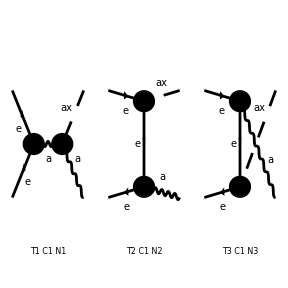

```mathematica
feeγALP=InsertFields[t22,{F[2,{1}],-F[2,{1}]}->{S[4],V[1]},InsertionLevel->{Classes},Model->ALPmodel,GenericModel->ALPmodel,
	ExcludeParticles->{V[2]}];
Paint[%];
```

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

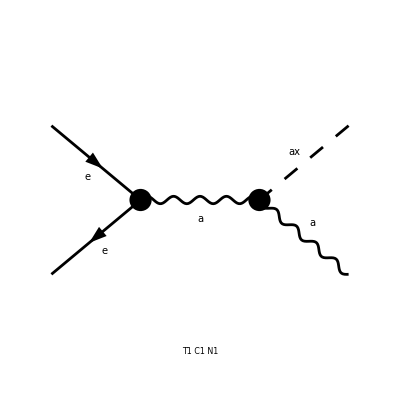

FeynArtsGraphics({e,e}→{ax,a})(([T1 C1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
DiagramExtract[feeγALP,1];
Paint[%]
```

```mathematica
AeeγALP=CreateFeynAmp[feeγALP];
AeeγALP11=CreateFeynAmp[DiagramExtract[feeγALP,1]];
AeeγALP22=CreateFeynAmp[DiagramExtract[feeγALP,2]];
AeeγALP33=CreateFeynAmp[DiagramExtract[feeγALP,3]];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

## No Spin

```mathematica
SetMandelstam[s,t,u,p1,p2,q1,q2,me,me,0,mA];
```

```mathematica
SP[p1+p2]//ExpandScalarProduct//Simplify
SP[p2,-q2]//ExpandScalarProduct//Simplify
SP[p2,-q1]//ExpandScalarProduct//Simplify
```

s

1/2 (mA^2+me^2-t)

1/2 (me^2-u)

#### Full Amplitude

```mathematica
FCFAConvert[AeeγALP,IncomingMomenta->{p1,p2},OutgoingMomenta->{q2,q1},DropSumOver->True,LorentzIndexNames->{μ,ν}]/.FCGV["ME"]->me/.FCGV["EL"]->e/.FeynAmpDenominator[PropagatorDenominator[Momentum[q1+q2],0]]->1/(SP[p1,p2]//ExpandScalarProduct//Simplify)/.FeynAmpDenominator[PropagatorDenominator[Momentum[p2-q2],Me]]->1/(SP[p2,-q2]//ExpandScalarProduct//Simplify)/.FeynAmpDenominator[PropagatorDenominator[Momentum[p2-q1],Me]]->1/(SP[p2,-q1]//ExpandScalarProduct//Simplify);
DiracSimplify[%,DiracSubstitute67->True]//Simplify;
Total[%]//Simplify;
1/4*FermionSpinSum[(%)(ComplexConjugate[%])]/.Me->me//DiracSimplify//Simplify;
DoPolarizationSums[%,q1,0]//Simplify;
Mtot=TrickMandelstam[%,{s,t,u,2 me^2+mA^2}]//Simplify
```

gc32^2 ((2 gc3 me s (mA^2-s)^2 (gc18L(1,1)-gc18R(1,1)))/((2 me^2-s) (me^2-u) (mA^2+me^2-t))-1/((me^2-u)^2 (mA^2+me^2-t)^2)2 s (-me^4 (12 mA^2 gc18L(1,1) gc18R(1,1)+19 s ((gc18L(1,1))^2+(gc18R(1,1))^2)+4 u (-4 gc18L(1,1) gc18R(1,1)+3 (gc18L(1,1))^2+3 (gc18R(1,1))^2))+me^2 (-(mA^2 (3 s ((gc18L(1,1))^2+(gc18R(1,1))^2)+2 u (gc18L(1,1)-gc18R(1,1))^2))+7 s^2 ((gc18L(1,1))^2+(gc18R(1,1))^2)+22 s u ((gc18L(1,1))^2+(gc18R(1,1))^2)+4 u (2 t gc18L(1,1) gc18R(1,1)-2 u gc18L(1,1) gc18R(1,1)+3 u (gc18L(1,1))^2+3 u (gc18R(1,1))^2))+u ((gc18L(1,1))^2+(gc18R(1,1))^2) (mA^2 (s+2 u)-3 s^2-7 s u-4 u^2)+4 me^6 (-4 gc18L(1,1) gc18R(1,1)+(gc18L(1,1))^2+(gc18R(1,1))^2))+(gc3^2 (mA^4 (2 me^2+s)-2 mA^2 s (me^2+s+u)+s (2 me^4-4 me^2 u+s^2+2 s u+2 u^2)))/((s-2 me^2)^2))

```mathematica
Expand[Mtot/.gc32->-e/.gc18L[1,1]->-(Cψ*me)/Subscript[f, a]/.gc18R[1,1]->(Cψ*me)/Subscript[f, a]/.gc3->Cγ/Subscript[f, a]]//Simplify
```

1/(f_a^2 (s-2 me^2)^2 (me^2-u)^2 (mA^2+me^2-t)^2)e^2 (Cγ^2 s^3 (me^2-u)^2 (mA^2+me^2-t)^2-2 Cγ^2 mA^2 s^2 (me^2-u)^2 (mA^2+me^2-t)^2+2 Cγ^2 s^2 u (me^2-u)^2 (mA^2+me^2-t)^2+2 Cγ^2 s u^2 (me^2-u)^2 (mA^2+me^2-t)^2-2 Cγ^2 mA^2 me^2 s (me^2-u)^2 (mA^2+me^2-t)^2-4 Cγ^2 me^2 s u (me^2-u)^2 (mA^2+me^2-t)^2-2 Cγ^2 mA^2 s u (me^2-u)^2 (mA^2+me^2-t)^2+2 Cγ^2 me^4 s (me^2-u)^2 (mA^2+me^2-t)^2+Cγ^2 mA^4 s (me^2-u)^2 (mA^2+me^2-t)^2+2 Cγ^2 mA^4 me^2 (me^2-u)^2 (mA^2+me^2-t)^2-4 Cγ Cψ me^2 s^3 (2 me^2-s) (me^2-u) (mA^2+me^2-t)+8 Cγ Cψ mA^2 me^2 s^2 (2 me^2-s) (me^2-u) (mA^2+me^2-t)-4 Cγ Cψ mA^4 me^2 s (2 me^2-s) (me^2-u) (mA^2+me^2-t)-4 Cψ^2 mA^2 me^2 s^2 u (s-2 me^2)^2-8 Cψ^2 mA^2 me^2 s u^2 (s-2 me^2)^2-24 Cψ^2 mA^2 me^6 s (s-2 me^2)^2+12 Cψ^2 mA^2 me^4 s^2 (s-2 me^2)^2+16 Cψ^2 mA^2 me^4 s u (s-2 me^2)^2+12 Cψ^2 me^2 s^3 u (s-2 me^2)^2+28 Cψ^2 me^2 s^2 u^2 (s-2 me^2)^2+16 Cψ^2 me^2 s u^3 (s-2 me^2)^2-48 Cψ^2 me^8 s (s-2 me^2)^2+76 Cψ^2 me^6 s^2 (s-2 me^2)^2+80 Cψ^2 me^6 s u (s-2 me^2)^2-28 Cψ^2 me^4 s^3 (s-2 me^2)^2-88 Cψ^2 me^4 s^2 u (s-2 me^2)^2+16 Cψ^2 me^4 s t u (s-2 me^2)^2-64 Cψ^2 me^4 s u^2 (s-2 me^2)^2)

#### 11

```mathematica
SP[p1,p2]//ExpandScalarProduct//Simplify
```

1/2 (s-2 me^2)

```mathematica
FCFAConvert[AeeγALP11,IncomingMomenta->{p1,p2},OutgoingMomenta->{q2,q1},DropSumOver->True,LorentzIndexNames->{μ,ν}]/.FCGV["ME"]->me/.FCGV["EL"]->e/.FeynAmpDenominator[PropagatorDenominator[Momentum[q1+q2],0]]->1/(SP[p1,p2]//ExpandScalarProduct//Simplify)
DiracSimplify[%,DiracSubstitute67->True]//Simplify;
Total[%]//Simplify;
1/4*FermionSpinSum[(%)(ComplexConjugate[%])]/.Me->me//DiracSimplify//Simplify;
DoPolarizationSums[%,q1,0]//Simplify;
M11=TrickMandelstam[%,{s,t,u,2 me^2+mA^2}]//Simplify
```

{(2 ⅈ gc3 (ḡ)^Lor3ν ((ε̄)^*)^μ(q1) (ϵ̄)^(OverBar[q1]OverBar[q1]+OverBar[q2]μLor3) (φ(-OverBar[p2],Me)).(ⅈ gc32 (γ̄)^ν.(γ̄)^6+ⅈ gc32 (γ̄)^ν.(γ̄)^7).(φ(OverBar[p1],Me)))/(s-2 me^2)}

(gc3^2 gc32^2 (mA^4 (2 me^2+s)-2 mA^2 s (me^2+s+u)+s (2 me^4-4 me^2 u+s^2+2 s u+2 u^2)))/((s-2 me^2)^2)

```mathematica
M11/.gc3->Cγ/Subscript[f, a]/.gc32->-e//Simplify
Expand[%*(Subscript[f, a]^2*(s-2*me^2)^2)/(Cγ^2*e^2)-C*(mA^4*(2*me^2+s)-2*mA^2*s*(mA^2+s+u)+s*(2*me^4-4*me^2*u+s^2+2*s*u+2*u^2))]//Simplify
```

(Cγ^2 e^2 (mA^4 (2 me^2+s)-2 mA^2 s (me^2+s+u)+s (2 me^4-4 me^2 u+s^2+2 s u+2 u^2)))/(f_a^2 (s-2 me^2)^2)

mA^4 ((C+1) s-2 (C-1) me^2)-2 mA^2 s (me^2-(C-1) (s+u))-(C-1) s (2 me^4-4 me^2 u+s^2+2 s u+2 u^2)

#### 22

```mathematica
FCFAConvert[AeeγALP22,IncomingMomenta->{p1,p2},OutgoingMomenta->{q2,q1},DropSumOver->True,LorentzIndexNames->{μ,ν}]/.FCGV["ME"]->me/.FCGV["EL"]->e/.FeynAmpDenominator[PropagatorDenominator[Momentum[p2-q1],Me]]->1/(SP[p2,-q1]//ExpandScalarProduct//Simplify);
DiracSimplify[%,DiracSubstitute67->True]//Simplify;
Total[%]//Simplify;
1/4*FermionSpinSum[(%)(ComplexConjugate[%])]/.Me->me//DiracSimplify//Simplify;
DoPolarizationSums[%,q1,0]//Simplify;
M22=TrickMandelstam[%,{s,t,u,2 me^2+mA^2}]//Simplify
```

-1/((me^2-u)^2)2 gc32^2 (2 mA^2 me^2 ((gc18L(1,1))^2+(gc18R(1,1))^2)+me^4 (-12 gc18L(1,1) gc18R(1,1)+(gc18L(1,1))^2+(gc18R(1,1))^2)-me^2 (3 t ((gc18L(1,1))^2+(gc18R(1,1))^2)+u (-4 gc18L(1,1) gc18R(1,1)+(gc18L(1,1))^2+(gc18R(1,1))^2))-t u ((gc18L(1,1))^2+(gc18R(1,1))^2))

```mathematica
M22/.gc32->-e/.gc18L[1,1]->-(Cψ*me)/Subscript[f, a]/.gc18R[1,1]->(Cψ*me)/Subscript[f, a]//Simplify
Expand[%*(Subscript[f, a]^2*(me^2-u)^2)/(Cψ^2*e^2*me^2)-C*((me^2-t)*(me^2-u)-2*mA^2*me^2)]//Simplify
```

-(4 Cψ^2 e^2 me^2 (2 mA^2 me^2+7 me^4-3 me^2 (t+u)-t u))/(f_a^2 (me^2-u)^2)

2 (C-4) mA^2 me^2-((C+28) me^4)+(C+12) me^2 (t+u)-(C-4) t u

#### 33

```mathematica
FCFAConvert[AeeγALP33,IncomingMomenta->{p1,p2},OutgoingMomenta->{q2,q1},DropSumOver->True,LorentzIndexNames->{μ,ν}]/.FCGV["ME"]->me/.FCGV["EL"]->e/.FeynAmpDenominator[PropagatorDenominator[Momentum[p2-q2],Me]]->1/(SP[p2,-q2]//ExpandScalarProduct//Simplify)
DiracSimplify[%,DiracSubstitute67->True]//Simplify;
Total[%]//Simplify;
1/4*FermionSpinSum[(%)(ComplexConjugate[%])]/.Me->me//DiracSimplify//Simplify;
DoPolarizationSums[%,q1,0]//Simplify;
M33=TrickMandelstam[%,{s,t,u,2 me^2+mA^2}]//Simplify
```

{(2 ((ε̄)^*)^μ(q1) (φ(-OverBar[p2],Me)).((γ̄)^7 gc18L(1,1)+(γ̄)^6 gc18R(1,1)).(γ̄·(OverBar[q2]-OverBar[p2])+Me).(ⅈ gc32 (γ̄)^μ.(γ̄)^6+ⅈ gc32 (γ̄)^μ.(γ̄)^7).(φ(OverBar[p1],Me)))/(mA^2+me^2-t)}

1/((mA^2+me^2-t)^2)2 gc32^2 (2 mA^2 me^2 (12 gc18L(1,1) gc18R(1,1)+5 (gc18L(1,1))^2+5 (gc18R(1,1))^2)+me^4 (28 gc18L(1,1) gc18R(1,1)+15 (gc18L(1,1))^2+15 (gc18R(1,1))^2)-me^2 (12 t gc18L(1,1) gc18R(1,1)+8 u gc18L(1,1) gc18R(1,1)+7 t (gc18L(1,1))^2+5 u (gc18L(1,1))^2+7 t (gc18R(1,1))^2+5 u (gc18R(1,1))^2)+t u ((gc18L(1,1))^2+(gc18R(1,1))^2))

```mathematica
M33/.gc32->-e/.gc18L[1,1]->-(Cψ*me)/Subscript[f, a]/.gc18R[1,1]->(Cψ*me)/Subscript[f, a]//Simplify
Expand[%*(Subscript[f, a]^2*(mA^2+me^2-t)^2)/(Cψ^2*e^2*me^2)-C*((me^2-t)*(me^2-u)-2*mA^2*me^2)]//Simplify
```

(4 Cψ^2 e^2 me^2 ((me^2-t) (me^2-u)-2 mA^2 me^2))/(f_a^2 (mA^2+me^2-t)^2)

(C-4) (2 mA^2 me^2-(me^2-t) (me^2-u))

## With Spin

```mathematica
FCFAConvert[Aeeμμ,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},DropSumOver->True,LorentzIndexNames->{μ,ν}]/.FCGV["ME"]->me/.FCGV["MM"]->mμ/.FCGV["EL"]->e;
DiracSimplify[%,DiracSubstitute67->True]//Simplify
(1/2)^4*%/.Spinor[Momentum[p1],me,1]->(1+s1*DiracGamma[5]).Spinor[Momentum[p1],me,1]/.Spinor[Momentum[p3],mμ,1]->Spinor[Momentum[p3],mμ,1].(1-s3*DiracGamma[5])/.Spinor[-Momentum[p2],me,1]->Spinor[-Momentum[p2],me,1].(1-s2*DiracGamma[5])/.Spinor[-Momentum[p4],mμ,1]->(1+s4*DiracGamma[5]).Spinor[-Momentum[p4],mμ,1]//Simplify;
Total[%]//DiracSimplify//Simplify
Simplify[FermionSpinSum[Contract[%ComplexConjugate[%]]]//DiracSimplify]/.(s1)^2->1/.(s2)^2->1/.(s3)^2->1/.(s4)^2->1//Simplify
test1=%/.s->4*Ebeam^2/.t->me^2+mμ^2+2*(Ebeam^2-Ebeam*Sqrt[Ebeam^2-mμ^2]*Cos[θ])/.u->me^2+mμ^2+2*(Ebeam^2+Ebeam*Sqrt[Ebeam^2-mμ^2]*Cos[θ])//Simplify
```

{-(e^2 (φ(-OverBar[p2],me)).(γ̄)^μ.(φ(OverBar[p1],me)) (φ(OverBar[p3],mμ)).(γ̄)^μ.(φ(-OverBar[p4],mμ)))/s}

-(e^2 ((s1 s2+1) (φ(-OverBar[p2],me)).(γ̄)^μ.(φ(OverBar[p1],me))+(s1+s2) (φ(-OverBar[p2],me)).(γ̄)^μ.(γ̄)^5.(φ(OverBar[p1],me))) ((s3 s4+1) (φ(OverBar[p3],mμ)).(γ̄)^μ.(φ(-OverBar[p4],mμ))+(s3+s4) (φ(OverBar[p3],mμ)).(γ̄)^μ.(γ̄)^5.(φ(-OverBar[p4],mμ))))/(16 s)

1/(2 s^2)e^4 (2 me^4 (s1 s2+1) (s3 s4+1)+2 me^2 (mμ^2 (s1 s2 (s3+s4)^2+2 s3 s4+2)+t (s1 (-s2 (s3 s4+1)+s3+s4)+s2 (s3+s4)-s3 s4-1)-u (s1 (s2 s3 s4+s2+s3+s4)+s2 (s3+s4)+s3 s4+1))+2 mμ^4 (s1 s2+1) (s3 s4+1)-2 mμ^2 (t (s1 (s2 s3 s4+s2-s3-s4)-s2 (s3+s4)+s3 s4+1)+u (s1 (s2 s3 s4+s2+s3+s4)+s2 (s3+s4)+s3 s4+1))+s1 s2 s3 s4 t^2+s1 s2 s3 s4 u^2+s1 s2 t^2+s1 s2 u^2-s1 s3 t^2+s1 s3 u^2-s1 s4 t^2+s1 s4 u^2-s2 s3 t^2+s2 s3 u^2-s2 s4 t^2+s2 s4 u^2+s3 s4 t^2+s3 s4 u^2+t^2+u^2)

(e^4 (4 Ebeam^4 (s1 s2+1) (s3 s4+1)+4 Ebeam^2 (Ebeam^2-mμ^2) cos^2(θ) (s1 s2+1) (s3 s4+1)+8 Ebeam^3 √(Ebeam^2-mμ^2) cos(θ) (s1+s2) (s3+s4)+me^2 mμ^2 s1 s2 (s3^2+s4^2-2)))/(16 Ebeam^4)

```mathematica
test1/.s1->+1/.s2->-1/.s3->+1/.s4->-1//Simplify
```

0

```mathematica
Simplify[test1/.s1->+1/.s2->+1/.s3->+1/.s4->+1,Assumptions->Ebeam>=0]
Simplify[%/.mμ->0,Assumptions->Ebeam>=0];
(%-e^4*(1+Cos[θ])^2)//Simplify
Simplify[test1/.s1->+1/.s2->+1/.s3->-1/.s4->-1,Assumptions->Ebeam>=0]
Simplify[%/.mμ->0,Assumptions->Ebeam>=0];
(%-e^4*(1-Cos[θ])^2)//Simplify
```

(e^4 ((Ebeam^2-mμ^2) cos^2(θ)+2 Ebeam √(Ebeam^2-mμ^2) cos(θ)+Ebeam^2))/Ebeam^2

0

(e^4 ((Ebeam^2-mμ^2) cos^2(θ)-2 Ebeam √(Ebeam^2-mμ^2) cos(θ)+Ebeam^2))/Ebeam^2

0

```mathematica
Simplify[test1/.s1->-1/.s2->-1/.s3->+1/.s4->+1,Assumptions->Ebeam>=0]
Simplify[%/.mμ->0,Assumptions->Ebeam>=0];
(%-e^4*(1-Cos[θ])^2)//Simplify
Simplify[test1/.s1->-1/.s2->-1/.s3->-1/.s4->-1,Assumptions->Ebeam>=0]
Simplify[%/.mμ->0,Assumptions->Ebeam>=0];
(%-e^4*(1+Cos[θ])^2)//Simplify
```

(e^4 ((Ebeam^2-mμ^2) cos^2(θ)-2 Ebeam √(Ebeam^2-mμ^2) cos(θ)+Ebeam^2))/Ebeam^2

0

(e^4 ((Ebeam^2-mμ^2) cos^2(θ)+2 Ebeam √(Ebeam^2-mμ^2) cos(θ)+Ebeam^2))/Ebeam^2

0